This notebook to test the conjectured relation
D_q^μ = D_q^ψ D_(1+(q-1)D_q^ψ)
between the local spectral dimension D_q^μ, the wavefunction dimension D_q^ψ and the global spectral dimension D_q. All dimensions are averaged over all sites and all wavefunctions.

This relation is verified in the perturbative limit ρ → 0 of the Fibonacci model. It is understood as a consequence of the fact that, in this limit, and for large systems, all but a negligible fraction of the wavefunctions are of the same fractal type.

## Definitions

Harper Hamiltonian at criticality (λ = 1).

```mathematica
(* Harper periodic *)
hharp[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(* Harper antiperiodic *)
hharpa[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*antiperiodic boundary conditions*)AppendTo[hopping,{1,q}->1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_]:=hharp[Fibonacci[n-2],Fibonacci[n-1]];
hfiba[n_]:=hharpa[Fibonacci[n-2],Fibonacci[n-1]];
```

We consider an infinite system, with a primitive cell consituted of F_n sites (n^th approximant). For this approximant we compute the bandwidths and the intensities of the eigenstates inside a primitive cell.

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBandsHarp[n_]:=IntBandsHarp[n]=Block[{vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hfib[n]];
{vpa,wfa}=Eigensystem[hfiba[n]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
(* averaged q moment of the intensity *)
avqIntHarp[q_,n_]:=avqIntHarp[q,n]=Total[IntBandsHarp[n][[1]]^q,2]/Fibonacci[n];
```

Compute the (averaged) wavefunction dimensions D_q^ψ

```mathematica
(* return a fit function f(x;q,n) = a x + b where a is -Subscript[τ, q]^ψ. nv is a list of approximant sizes used to do the fit *)
linFitHarp[q_,nv_]:=Block[{avIntN,data},
avIntN=Map[avqIntHarp[q,#]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

Compute the (averaged) local spectral dimensions D_q^μ

```mathematica
(* averaged Γ^μ *)
avqIntHarp[τ_,q_,n_]:=avqIntHarp[τ,q,n]=Total[(IntBandsHarp[n][[2]])^-τ Total[IntBandsHarp[n][[1]]^q]]/Fibonacci[n];
```

```mathematica
tauHarp[q_,n_]:=τ/.FindRoot[avqIntHarp[τ,q,n]/avqIntHarp[τ,q,n-3]-1,{τ,0.}]
```

Compute the global spectral dimensions D_q

```mathematica
(* Γ *)
GamHarp[τ_,q_,n_]:=GamHarp[τ,q,n]=Total[(IntBandsHarp[n][[2]])^-τ Fibonacci[n]^-q];
```

```mathematica
tauSpec[q_,n_]:=τ/.FindRoot[GamHarp[τ,q,n]/GamHarp[τ,q,n-3]-1,{τ,0.}]
```

## Computations

### Considerations on the n dependance of the thermodynamic functions χ, Γ and τ.

We see that χ^ψ and Γ^μ exhibit a fluctuation that depends on n (mod 3).

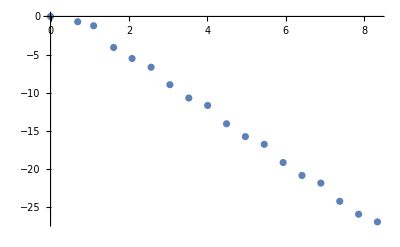

```mathematica
(* χ as a function of n for a given q *)
nValues=Range[2,19,1];
avIntN=Map[avqIntHarp[15.,#]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

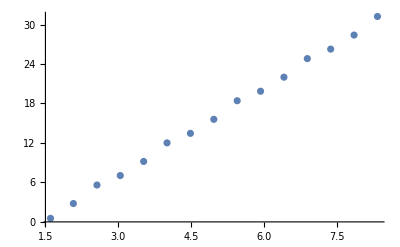

```mathematica
(* Γ as a function of n for given q and τ *)
τ=3.;
nValues=Range[5,19,1];
avIntN=Map[avqIntHarp[τ,10.,#]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

Because of the 3-periodicity, we compute Γ^n/Γ^(n-3) rather than Γ^n/Γ^(n-1).
The computed value τ_q^n itself depends on n (mod 3).

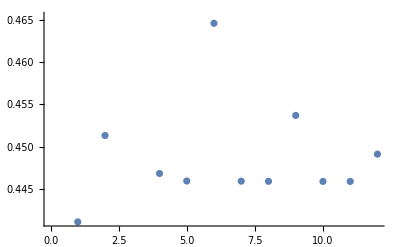

```mathematica
(* τ as a function of n for a given q *)
nValues=Range[8,19,1];
ListPlot[tauHarp[3.,#]&/@nValues]
```

We see that the function is better converged for n = 0, 2 (mod 3). We will thus chose these value of n in the future.

### Computations

#### D^ψ

We first chose a reasonable range of values for q. We avoid q<0 because on numerical problems (q<0 is sensible to small coefficients, which are not computed accurately).

```mathematica
qValues=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5]~Join~Range[20.,50.,2.];
```

For the computation of χ, we need a range of values of n on which we will do the log-log linear fit. As discussed before, we chose n (mod 3) = 0 or 2, and we also want n to be the largest possible, in what is achievable numerically.
This imposes n = 12, 15, 18.

```mathematica
nValues={12,15,18};
```

```mathematica
(* Compute the fits *)
fitsHarp=linFitHarp[#,nValues]&/@qValues;
```

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqsPsi=-Normal[#["ParameterTable"]][[1,3,2]]&/@fitsHarp;
(* convert to Subscript[D, q]^ψ *)
dqsPsi=MapThread[#1/(#2-1)&,{tauqsPsi,qValues}];
```

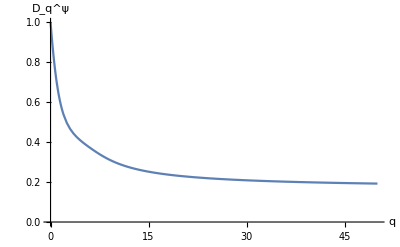

```mathematica
ListPlot[glue[qValues,dqsPsi],Joined->True,AxesLabel->{"q","D_q^ψ"}]
```

#### Comparison

For comparison, we also try n (mod 3) = 1, ie
This imposes n = 13, 16, 19.

```mathematica
nValues={13,16,19};
```

```mathematica
(* Compute the fits *)
fitsHarp=linFitHarp[#,nValues]&/@qValues;
```

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqsPsi=-Normal[#["ParameterTable"]][[1,3,2]]&/@fitsHarp;
(* convert to Subscript[D, q]^ψ *)
dqsPsiComp=MapThread[#1/(#2-1)&,{tauqsPsi,qValues}];
```

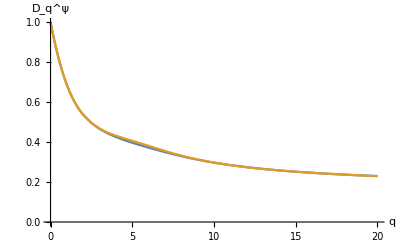

```mathematica
ListPlot[glue[qValues,#]&/@{dqsPsi,dqsPsiComp},Joined->True,AxesLabel->{"q","D_q^ψ"}]
```

#### D^μ

```mathematica
(* n(mod 3) = 0 *)
nValue=18;
τausMu=tauHarp[#,nValue]&/@qValues;
dqsMu=τausMu/(qValues-1);
```

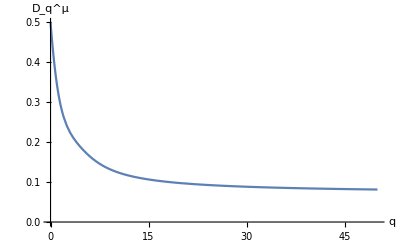

```mathematica
ListPlot[glue[qValues,dqsMu],Joined->True,AxesLabel->{"q","D_q^μ"}]
```

#### D

We want to check the conjecture
D_q^μ=D_q^ψ D_(1+(q-1)D_q^ψ)
It remains to compute D_q' for q’ in the range 1+(q-1)D_q^ψ, q ∈ qValues.

```mathematica
(* range of values of q over which Subscript[D, q] is computed *)
qVSpec=1+(qValues-1)dqsPsi;
τausSpec=tauSpec[#,nValue]&/@qVSpec;
dqsSpec=τausSpec/(qVSpec-1);
```

Notice how D_q varies veeeery slowly with q.

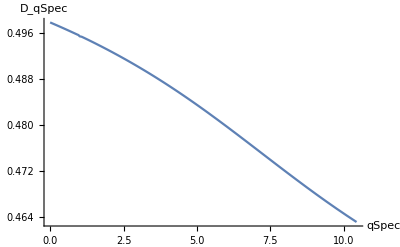

```mathematica
ListPlot[glue[qVSpec,dqsSpec],Joined->True,AxesLabel->{"qSpec","D_qSpec"}]
```

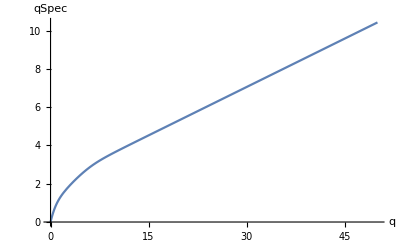

```mathematica
ListPlot[glue[qValues,qVSpec],Joined->True,AxesLabel->{"q","qSpec"}]
```

#### Test relation

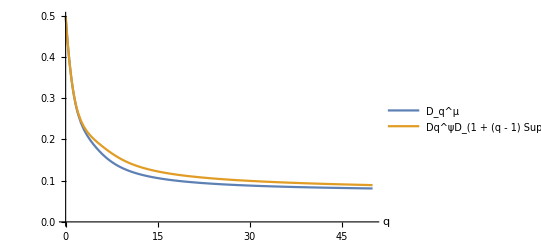

```mathematica
ListPlot[glue[qValues,#]&/@{dqsMu,dqsPsi*dqsSpec},Joined->True,AxesLabel->{"q"},PlotLegends->{"D_q^μ","Dq^ψD_(1 + (q - 1) SuperscriptBox[SubscriptBox[D, q], ψ])"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/relation.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Harper/data/relation.pdf